```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
data=Import["triplet_soln.txt","Table"];
```

```mathematica
hdata=Select[data,#[[2]]=="h"&][[;;,3]];
jdata=Select[data,#[[2]]=="J"&][[;;,3]];
kdata=Select[data,#[[2]]=="K"&][[;;,3]];
```

```mathematica
hinit=-2.99927;
jinit=0.0612041;
kinit=2.77309;
```

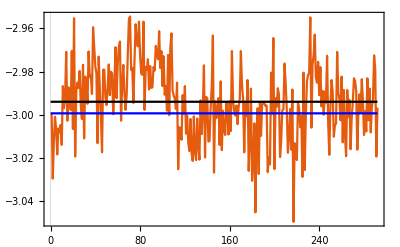

```mathematica
Show[
ListLinePlot[hdata],
ListLinePlot[{{0,Mean[hdata]},{Length[hdata],Mean[hdata]}},PlotStyle->Black],
ListLinePlot[{{0,hinit},{Length[hdata],hinit}},PlotStyle->Blue]
]
```

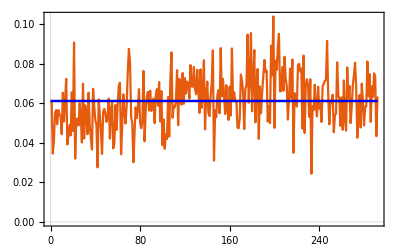

```mathematica
Show[
ListLinePlot[jdata],
ListLinePlot[{{0,Mean[jdata]},{Length[jdata],Mean[jdata]}},PlotStyle->Black],
ListLinePlot[{{0,jinit},{Length[jdata],jinit}},PlotStyle->Blue]
]
```

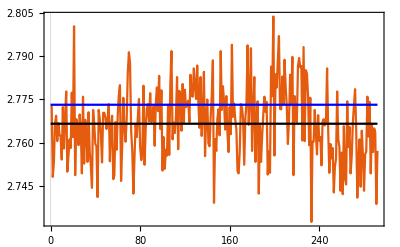

```mathematica
Show[
ListLinePlot[kdata],
ListLinePlot[{{0,Mean[kdata]},{Length[kdata],Mean[kdata]}},PlotStyle->Black],
ListLinePlot[{{0,kinit},{Length[kdata],kinit}},PlotStyle->Blue]
]
```